#### Note: The DOS code given here is derived from band data, is not an accurate self-consistent result, and only shows the result as a plot.

#### Processing Data

```mathematica
(*Data generated from VASPKIT.*)
(*Read the band data file*)
SetDirectory[FileNameTake[NotebookFileName[],{1,-2}]];
banddata1=Import["PBAND_C.dat","Table"];
banddata2=Select[banddata1,# ≠ {} && Characters[#][[1,1]] ≠ "#" &];
NKPTS=banddata1[[2,5]](*The number of K-dots on each band*)
NBANDS=banddata1[[2,6]](*Number of bands*)
Array[band,NBANDS];
Table[band[i+1]=Sort[banddata2[[i*NKPTS+1;;(i+1)*NKPTS]],#1[[1]]<#2[[1]]&],{i,0,NBANDS-1}];
orb=<|Table[banddata1[[1]][[n]]->n,{n,1,Length[banddata1[[1]]]}]|>
```

200

40

<|#K-Path→1,Energy→2,s→3,p→4,d→5,tot→6|>

```mathematica
(*Read the KPOINTS file*)
kpoints=Select[Import["KPOINTS","Table"],# ≠ {} && Characters[#][[1,1]] ≠ "#" &];
KPTS=NKPTS/kpoints[[2,1]](*The number of high-symmetry points*)
Array[K,KPTS];
Table[K[i]=Transpose[band[1]][[1,kpoints[[2]]*i]][[1]],{i,1,KPTS}];
KK=Table[{K[i],kpoints[[4+2*i,4]]},{i,1,KPTS}];
PrependTo[KK,{K[0]=Transpose[band[1]][[1,1]],kpoints[[5,4]]}];
KK=KK/.{"GAMMA"->"Γ"}(*The positions and names of high-symmetry points*)
```

2

{{0.,M},{1.46937,G},{3.16605,K}}

#### Total band and total density of state (TBAND and TDOS)

```mathematica
Array[tband,NBANDS];
Table[tband[i]=Transpose@((Transpose@band[i])[[1;;2]]),{i,1,NBANDS}];
```

```mathematica
(*Band structure: easy to view the band number index*)
ListLinePlot[Table[Tooltip[tband[i]],{i,1,NBANDS}],
Axes->False,GridLines->{Transpose[KK][[1]],{0}},
GridLinesStyle->Directive[Orange, Dashed],
Frame->True,FrameTicks->{{Automatic,None},{KK,None}},
FrameStyle->Directive[Purple],
FrameLabel->{"Wave vector","Energy(eV)"},
AspectRatio->5/3,
PlotStyle->Directive[Thick],
PlotRange->{{K[0],K[KPTS]},{-15,15}},
PlotLabels->Table[i,{i,1,NBANDS}]]
```

-Graphics-

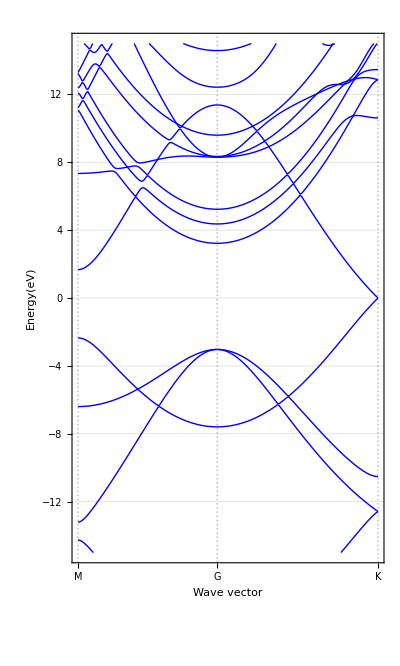

```mathematica
bandfig=ListLinePlot[Table[Tooltip[tband[i]],{i,1,NBANDS}],
Axes->False,
Frame->True,FrameTicks->{{Automatic,None},{KK,None}},
FrameStyle->Directive[Purple],
FrameLabel->{"Wave vector","Energy(eV)"},
AspectRatio->5/3,
PlotStyle->Directive[Blue,Thick],
PlotRange->{{K[0],K[KPTS]},{-15,15}},
PlotTheme->"Detailed"]
```

```mathematica
(*Define a function that solves the TDOS*)
(*The required data are band[i] and NBANDS, which correspond to the specific data of each PBAND and the total number of bands, respectively.*)
(*tdosdata[TEnergy_,round_]:The number of columns and rounding values corresponding to the energy need to input*)
tdosdata[TEnergy_,round_]:=Module[{a=TEnergy,b=round,t},
t={};
Table[AppendTo[t,Transpose[band[i]][[a]]],{i,1,NBANDS}];
Tally[Round[Sort@Flatten@t,b]]
]
```

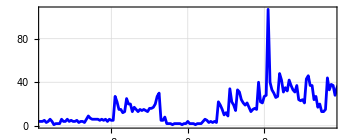

```mathematica
ListLinePlot[tdosdata[{2},0.2],PlotStyle->Blue,PlotTheme->"Detailed",
PlotRange->{{-15,15},{All,All}},AspectRatio->2/5]
```

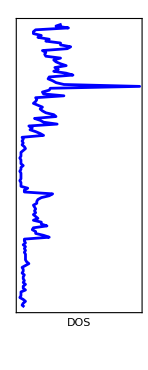

```mathematica
dosfig=ListLinePlot[Transpose@RotateLeft@Transpose@tdosdata[{2},0.2],
PlotStyle->Blue,PlotTheme->"Detailed",PlotRange->{{All,All},{-15,15}},
AspectRatio->5/2,FrameLabel->{"DOS",None},FrameTicks->None]
```

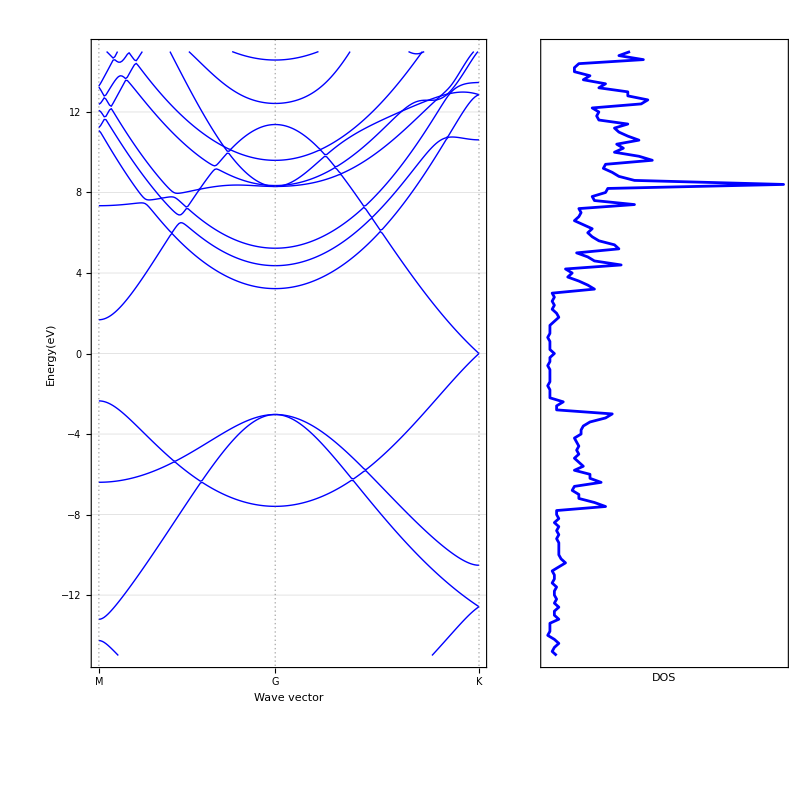

```mathematica
GraphicsRow[{bandfig,dosfig},1]
```

#### Projected band and Projected density of state (PBAND and PDOS)

```mathematica
pbnd[orbitals_,color_:Red,legend_:"orbitals",scaling_:10]:=
Graphics[Table[{PointSize[Sum[band[j][[i,orbitals[[k]]]],{k,Length[orbitals]}]/scaling],
color,
Tooltip[Point[{band[j][[i,1]],band[j][[i,2]]}]]},{j,1,NBANDS},{i,1,NKPTS}],
Axes->False,GridLines->{Transpose[KK][[1]],{0}},GridLinesStyle->Directive[Orange, Dashed],
Frame->True,FrameTicks->{{Automatic,None},{KK,None}},
FrameStyle->Directive[Black],FrameLabel->{"Wave vector","Energy(eV)"},
AspectRatio->5/3,
PlotRange->{{K[0],K[KPTS]},{-15,15}},PlotRangeClipping->True]
```

```mathematica
(*The 3rd column corresponds to the s-orbital, and the 4th column corresponds to the p-orbital*)
pbandfig=Show[pbnd[{3},Green,"s",20],pbnd[{4},Purple,"p",20]]
```

```mathematica
(*Define a function for solving the PDOS*)
(*The required data are band[i] and NBANDS, which correspond to the specific data of each PBAND and the total number of bands, respectively.*)
(*pdosdata[EnergyWeight_,round_]:The number of columns and rounding values corresponding to the energy need to input*)
pdosdata[EnergyWeight_,round_]:=Module[{a=EnergyWeight,b=round,p},
Array[pband,NBANDS];
Table[pband[i]=Transpose[Transpose[band[i]][[a]]],{i,1,NBANDS}];
pTband=Flatten[Table[pband[i],{i,1,NBANDS}],1]//Sort;
lst1=Transpose[pTband][[1]];
lst2=Transpose[pTband][[2]];
tally=Tally[Round[lst1,b]];
tally1=Transpose[tally][[1]];
tally2=Transpose[tally][[2]];
p={Total[lst2[[1;;tally2[[1]]]]]};
Table[AppendTo[p,Total[lst2[[Total[tally2[[1;;i-1]]];;Total[tally2[[1;;i]]]]]]],
{i,2,Length[tally2]}];
Transpose[{tally1,p}]]
```

```mathematica
ListLinePlot[{pdosdata[{2,3},0.2],pdosdata[{2,4},0.2]},PlotStyle->{Green,Purple},
PlotTheme->"Detailed",PlotRange->{{-15,15},{All,All}},
AspectRatio->2/5,
PlotLegends->{"s","p"}]
```

```mathematica
pdosdata1=Transpose@RotateLeft@Transpose@pdosdata[{2,3},0.2];
pdosdata2=Transpose@RotateLeft@Transpose@pdosdata[{2,4},0.2];
pdosfig=ListLinePlot[{pdosdata1,pdosdata2},PlotStyle->{Green,Purple},
PlotTheme->"Detailed",PlotRange->{{All,All},{-15,15}},
AspectRatio->5/2,FrameLabel->{"DOS",None},FrameTicks->None]
```

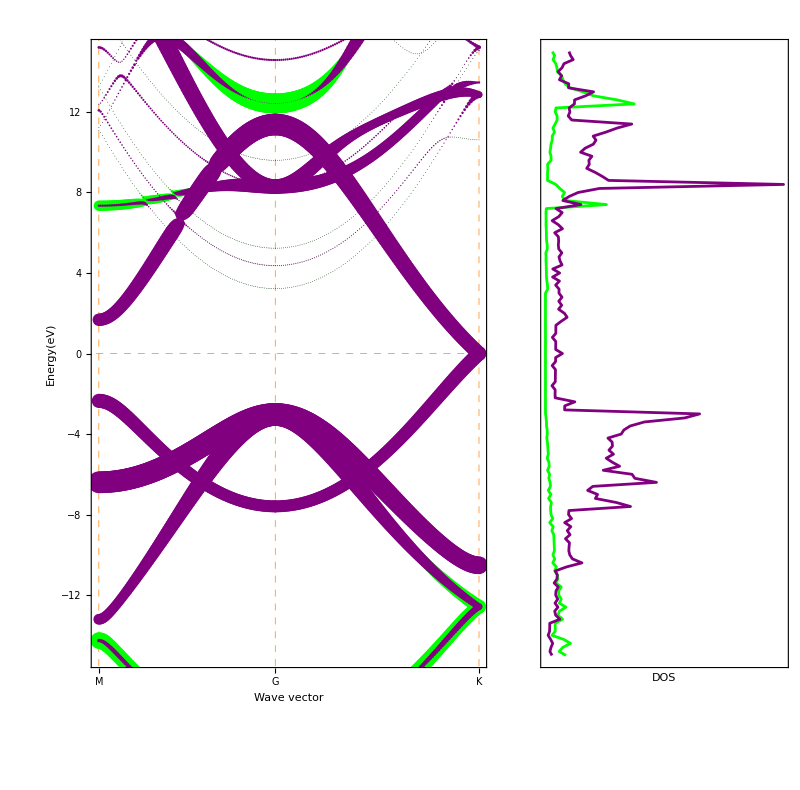

```mathematica
GraphicsRow[{pbandfig,pdosfig},1]
```

#### Different types of Figures

```mathematica
pbndtest1[orbitals_,color_:Red,scaling1_:10,scaling2_:5]:=Graphics[
Table[{Directive[
PointSize[Sum[band[j][[i,orbitals[[k]]]],{k,Length[orbitals]}]/scaling1],
Opacity[Sum[band[j][[i,orbitals[[k]]]],{k,Length[orbitals]}]/scaling2]],
color,
Tooltip[Point[{band[j][[i,1]],band[j][[i,2]]}]]},{j,1,NBANDS},{i,1,NKPTS}],
Axes->False,GridLines->{Transpose[KK][[1]],{0}},GridLinesStyle->Directive[Orange, Dashed],
Frame->True,FrameTicks->{{Automatic,None},{KK,None}},FrameStyle->Directive[Black],
FrameLabel->{"Wave vector","Energy(eV)"},AspectRatio->5/3,
PlotRange->{{K[0],K[KPTS]},{-15,15}},PlotRangeClipping->True]
```

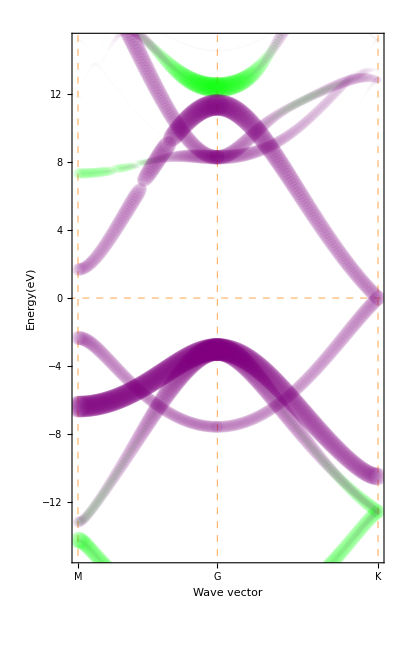

```mathematica
Show[pbndtest1[{3},Green,20,5],pbndtest1[{4},Purple,20,5]]
```

```mathematica
pbndtest2[orbitals_,color_:Red,scaling_:5]:=Graphics[
Table[{Directive[
Opacity[Sum[band[j][[i,orbitals[[k]]]],{k,Length[orbitals]}]/scaling]],
color,
Tooltip[Point[{band[j][[i,1]],band[j][[i,2]]}]]},{j,1,NBANDS},{i,1,NKPTS}],
Axes->False,GridLines->{Transpose[KK][[1]],{0}},GridLinesStyle->Directive[Orange, Dashed],
Frame->True,FrameTicks->{{Automatic,None},{KK,None}},FrameStyle->Directive[Orange,12],
FrameLabel->{"Wave vector","Energy(eV)"},AspectRatio->5/3,
PlotRange->{{K[0],K[KPTS]},{-15,15}},PlotRangeClipping->True,
Background->Black]
```

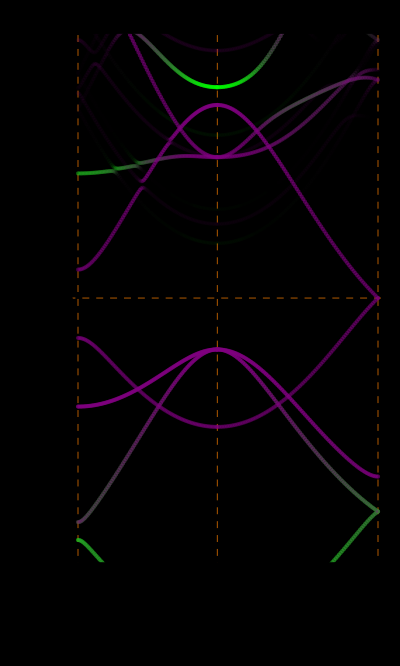

```mathematica
Show[pbndtest2[{3},Green,1],pbndtest2[{4},Purple,1]]
```